V2: I try to import the .m file of the original file. Then here I can modify all the nonsense I want.

I start with contracting the vertices in config. space to get nice drawings (hopefully).
This should not be much different than what I have already done for the LRW/DLA actions.

INDEX ORDER MODIFIED TO TAKE CARE OF 0,1,2 OR EVEN MORE INDICES AUTOMATICALLY

```mathematica
<<"D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\Diagrams\Diagrams-V1.m";
```

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: myFavoriteGraph is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

General::stop: Further output of PropertyValue::argr will be suppressed during this calculation.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

# Graphics

## Notations

```mathematica
Needs["Notation`"]
Notation[Subscript[β, a__] ⟺ β[a__]]
Notation[Subscript[R, a__] ⟺ R[a__]]
Notation[Subscript[ϕ, a__] ⟺ ϕ[a__]]
Notation[Subscript[χ, a__] ⟺ χ[a__]]
Notation[Subscript[ψ, a__] ⟺ ψ[a__]]
Notation[Subscript[ξ, a__] ⟺ ξ[a__]]
Notation[(ϕ^*)_a__ ⟺ ϕs[a__]]
Notation[(χ^*)_a__ ⟺ χs[a__]]
Notation[(ψ^*)_a__ ⟺ ψs[a__]]
Notation[(ξ^*)_a__ ⟺ ξs[a__]]
Notation[ϕ^* ⟺ ϕs]
{{Notation[χ^* ⟺ χs]}, {Notation[ψ^* ⟺ ψs]
Notation[ξ^* ⟺ ξs]}}
```

{{Null},{Null^2}}

### Test Notation

```mathematica
V[a]
```

V[a]

```mathematica
β[1,2]
```

β_(1,2)

## MyGraph[]

```mathematica
Clear[MyGraph];
Options[MyGraph]={"undirected" ->True,"label" ->False};
MyGraph[edges__,root_,source_,OptionsPattern[]]:={Module[{locEdges={},i,locWeights={},locRoot=root,locSource=source,p},
Clear[β];

For[i=1, i<=(Dimensions@edges)[[1]],i++,
If[OptionValue["undirected"] && edges[[i,2]] =!=locSource && edges[[i,2]] =!=edges[[i,1]] ,
AppendTo[locEdges,edges[[i,2]]->edges[[i,1]]];
AppendTo[locWeights,β[edges[[i,2]],edges[[i,1]]] ]
];

If[edges[[i,1]]==locSource,Continue[]];

AppendTo[locEdges,edges[[i,1]]->edges[[i,2]]];
AppendTo[locWeights,β[edges[[i,1]],edges[[i,2]]] ]
];

locEdges=Sort[locEdges,(#1[[1]]<=#2[[1]] &&#1[[2]]<=#2[[1]])||(#1[[1]]<#2[[2]] &&#1[[2]]<=#2[[2]]) &];

p[β[a_,b_],β[c_,d_]]:=1/;(a<=c&&b<=c);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<=a&&d<=a);
p[β[a_,b_],β[c_,d_]]:=1/;(a<d&&b<=d);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<b&&d<=b);
locWeights=Sort[locWeights,p];

(*Print[locEdges];
Print[locWeights]*);

If[ OptionValue["label"],
(*True*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, EdgeLabels->"EdgeWeight", VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]]
],
root(*Root*),source(*Source*)}
```

### Usage example of MyGraph[]

“edges” must be a list of ordered pairs containing the vertices of the graph. The edge is intended from the first vertex to the second.
If “directed” is false (optional, default to true), then a undirected graph is drawn

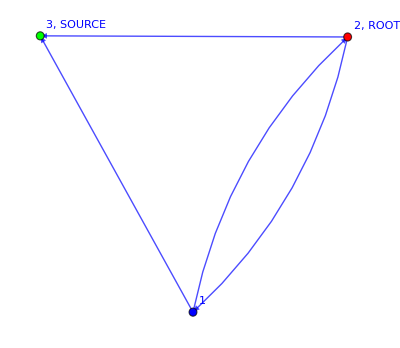

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]]
```

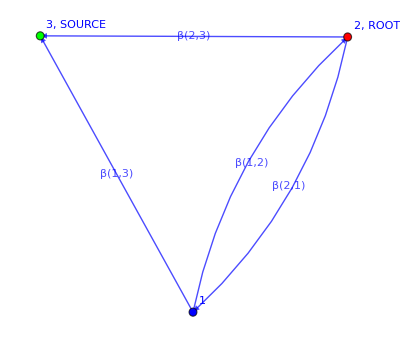

```mathematica
gLabel=MyGraph[edges,root,source,"printEdgesLabel"->True]
```

## DrawOnGraph[]

“Path” should be made of triplets whose first two elements are the initial and final vertices respectively, while the last is the color of this edge

```mathematica
Clear[DrawOnGraph];
Options[DrawOnGraph]={"drawOthers"-> True};
DrawOnGraph[graph_,path__,OptionsPattern[]]:=Module[{locEdges,locPathStyle={},locRoot,locSource,i},
locEdges = EdgeList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

For[i=1, i<=Length[path],i++,
AppendTo[locPathStyle,{path[[i,1]]->path[[i,2]]->path[[i,3]]}];
(*Print[locPathStyle]*)
];
If[OptionValue["drawOthers"],
(*True*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,Blue}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,White}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]
]
]
```

### Usage example of DrawOnGraph[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW

```mathematica
path1={{2,1,Red},{1,3,Green}};
DrawOnGraph[g,path1]
```

PropertyValue::pvobj: myFavoriteGraph is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: myFavoriteGraph is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

Graph[EdgeList[myFavoriteGraph],EdgeStyle→{2->1→RGBColor[1, 0, 0],1->3→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},VertexLabels→{PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,ROOT,PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,SOURCE,Name},VertexStyle→{PropertyValue[]⟦1⟧→RGBColor[1, 0, 0],PropertyValue[]⟦1⟧→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

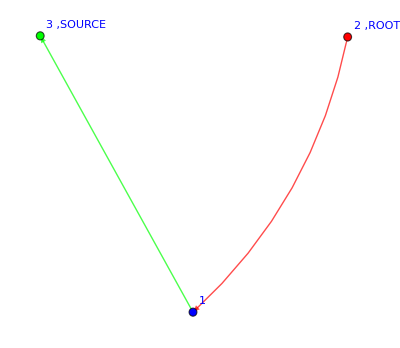

```mathematica
DrawOnGraph[g,path1,"drawOthers"->False]
```

## DrawFromExpression[]

```mathematica
Clear[DrawFromExpression];
Options[DrawFromExpression]={"graph"->g,"drawOthers"->False};

DrawFromExpression[exp_,OptionsPattern[]]:=Module[{terms,graphs={},i},
terms=exp//.R[a_,b_,c_]^n_->R[a,b,c]//Expand;
terms=List @@ (terms+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->OptionValue["drawOthers"]]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];
]
```

## AugmentedGraph[]

This is useful to compute the total incoming current from the source towards the DLA cluster/Tree. WE MUST ADD THE EDGE FROM THE OLD SOURCE TO THE NEW SOURCE, AS WELL AS ALLOW THE EDGES FROM THE OLD SOURCE TO THE NEIGHBORS

```mathematica
Clear[AugmentedGraph];
AugmentedGraph[graph_]:=Module[{locVertices,locEdges,locPathStyle={},locRoot,locSource,newSource,oldSourceNeighbors,graphPlus,i},

locVertices = VertexList@graph;
locEdges = EdgeList@graph/.DirectedEdge->List;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

newSource=locVertices[[-1]]+1;

(*Add the edge from the oldSource to the newSource*)
AppendTo[locEdges,{locSource,newSource}];

(*Add all the edges from the oldSource to its neighbors*)
oldSourceNeighbors=Select[locEdges, #[[2]]==locSource &];

For[i=1,i<=Length[oldSourceNeighbors],i++,
AppendTo[locEdges,{locSource,oldSourceNeighbors[[i,1]]}]
];

graphPlus =MyGraph[locEdges,locRoot,newSource,"undirected"->False][[1]];

Return[{graphPlus,locSource,newSource}]
]
```

#### Usage example of AugmentedGraph[]

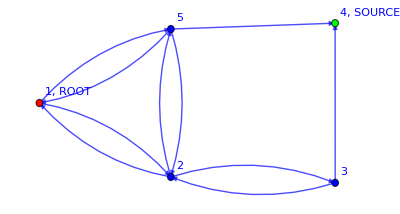

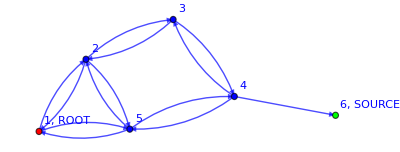
{-Graphics-,4,6}

```mathematica
g=myFavoriteGraph
AugmentedGraph[g]
```

# Field Theory tools

## monoFlatten[]

```mathematica
Clear[monoFlatten];
(*monoFlatten[a_?NumericQ]:={};*)
monoFlatten[a_]:={a};
monoFlatten[{a__}]:={{a}};
monoFlatten[{a__,b__}]:={a,b};
```

#### Test

## ExtractPaths[]

```mathematica
(*To extract the paths and their weights from the expression of an expectation value*)
```

```mathematica
Clear[ExtractPaths];
ExtractPaths[exp_]:=Module[{terms,paths={},i},

terms=exp//Expand;
terms=List @@Collect[terms,R[__,Red]];
terms=Outer[List,terms];

For[i=1,i<=Length[terms],i++,
If[MatchQ[terms[[i,1]],R[__,Red]*A_],
AppendTo[paths,terms[[i]]]
]
];
terms=paths//.R[__,Blue]->1//FullSimplify;

Return[terms]
]
```

#### Usage example of ExtractPaths[]

```mathematica
exp=(1-(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 2,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 5,2])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])));ExtractPaths[exp]
```

{{(R_(1,2,RGBColor[1, 0, 0]) β_(1,2) (β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))},{(R_(1,5,RGBColor[1, 0, 0]) β_(1,5) ((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))}}

## Laplacian DD[] rules

```mathematica
ClearAll[DD];
(*Remove[DD];*)
DD[0]=0;
DD'[(κ*A_+B_)C_]:=DD[A*C]/(A*C);
(*DD'[a_[x_] b_[y_]]:=1;
DD[a_[x_]*b_[y_]]:=DD[a[x]]*b[y]+DD[b[y]]*a[x]+2∇a[x]*∇b[y];*)
```

#### Tests

```mathematica
DD'[ϕ[x] χ[x]]
```

1

```mathematica
V[DD[ϕ[x] χ[x]]]/.ϕ[x_]->ϕ[x]+κ δϕ[x]
D[%,κ]
%/.κ->0
```

V[DD[(κ δϕ[x]+ϕ[x]) χ[x]]]

DD[δϕ[x] χ[x]]

DD[δϕ[x] χ[x]]

## Vertex rules

The vertices are where the interaction takes place in the field theory.

```mathematica
ClearAll[V];
V[1.]:=1.;
V[1]:=1;
V[0]:=0;
(*V'[DD[a__]]:=DD[a]/a;(*(ToExpression["δ"<>ToString[a]]);*)*)
V'[a_]:=1;
```

## δrules

```mathematica
ClearAll[Σδrule];
Σδrule={δ[a_,b_]^n_/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,b]^(n-2)δ[a,a],
δ[b_,a_]δ[c_,b_]/;(!NumericQ[b] && !MatchQ[b,Subscript[1, __]]):>δ[c,a],
δ[a_,b_]δ[c_,b_]/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,c],

δ[a_,a_]/;(MatchQ[a,Subscript[i, __]])/;(a=!=Subscript[i, s]):>Subscript[n, χ],
δ[a_,a_]/;(MatchQ[a,Subscript[α, __]]):>Subscript[n, α]};
```

```mathematica
ClearAll[δruleExternal]
(*δruleExternal={δ[a_,a_]/;(NumericQ[a] || a==Subscript[i, s] || MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[a,Subscript[1, __]]||MatchQ[a,Subscript[k, _]]):>1,
δ[a_,b_]/;(NumericQ[a] ||MatchQ[a,Subscript[k, _]]|| MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[a,Subscript[1, _]])/;(a=!=b):>0,
δ[a_,b_]/;(NumericQ[b] ||MatchQ[b,Subscript[k, _]]|| MatchQ[b,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[b,Subscript[1, _]])/;(a=!=b):>0 };*)
```

### Usage examples of the δrules

```mathematica
δ[b,a]δ[c,b]/.Σδrule
```

δ[c,a]

```mathematica
δ[b,a]δ[a,b]//.Σδrule
```

n

```mathematica
δ[b,a]δ[c,a]δ[c,b]//.Σδrule
```

n

```mathematica
δ[1,i]δ[i,1]//.Σδrule//.δruleExternal
```

1

```mathematica
δ[1,i]δ[i,2]//.Σδrule//.δruleExternal
```

0

```mathematica
δ[1,i]δ[i,1]δ[a,b]δ[a,b]//.Σδrule//.δruleExternal
```

δ[a,a]

```mathematica
δ[Subscript[k, 1],Subscript[k, 1]]//.Σδrule
```

m

```mathematica
δ[Subscript[i, 1],Subscript[i, 1]]//.Σδrule
```

n

```mathematica
δ[Subscript[j, -1],Subscript[j, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[k, -1],Subscript[k, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[1, 1],Subscript[1, -1]]δ[Subscript[1, 1],Subscript[1, -1]]//.Σδrule
```

δ[1_1,1_-1]^2

## FieldsNamesGenerator[]

```mathematica
Clear[FieldsNamesGenerator];
FieldsNamesGenerator[fields_]:=
FieldsNamesGenerator[fields]=Block[{locFields={},starFields={},deltaFields={},deltaStarFields={},l},

locFields=fields;

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

Return[{locFields,starFields,deltaFields,deltaStarFields}]
]
```

#### Test

```mathematica
fields={ϕ,χ};
FieldsNamesGenerator[fields]//AbsoluteTiming
FieldsNamesGenerator[fields]//AbsoluteTiming
```

{0.0000616,{{ϕ,χ},{ϕ^*,χ^*},{δϕ,δχ},{δϕs,δχs}}}

{3.1×10^-6,{{ϕ,χ},{ϕ^*,χ^*},{δϕ,δχ},{δϕs,δχs}}}

# Vertices contraction

## FreeAction[]

```mathematica
ClearAll[FreeAction];

FreeAction[time_]:=V[Exp[ψs[Subscript[x, ToExpression["action"<>ToString[ time]]],Subscript[t, time+1]]ψ[Subscript[x, ToExpression["action"<>ToString[ time]]],Subscript[t, time]]]];
```

## SpaceVertices definition

```mathematica
ClearAll[Vγ1,Vγ1Minus,Vγ1gχ,Vγ1gχMinus,Vγ1gψ,Vγ1gψMinus,Vγ2,Vγ2Minus,Vγ2gχ,Vγ2gχMinus,Vγ2gψ,Vγ2gψMinus,Vψψ,Vψχ,Vχχ,g];

Vγ1[space_,time_]:= V[γ1 ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];
Vγ1Minus[space_,time_]:= V[-γ1 ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]];

Vγ1gχ[space_,time_]:= V[γ1g ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];
Vγ1gχMinus[space_,time_]:= V[-γ1g ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];

Vγ1gψ[space_,time_]:= V[γ1g ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]];
Vγ1gψMinus[space_,time_]:= V[-γ1g ϕ[space,Subscript[t, time]]χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]];


Vγ2[space_,time_]:= V[γ2 ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]ψs[space,Subscript[t, time+1]]];
Vγ2Minus[space_,time_]:= V[-γ2 ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]]ϕs[space,Subscript[t, time+1]]];

Vγ2gχ[space_,time_]:= V[γ2g ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]ψs[space,Subscript[t, time+1]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];
Vγ2gχMinus[space_,time_]:= V[-γ2g ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];

Vγ2gψ[space_,time_]:= V[γ2g ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]ψs[space,Subscript[t, time+1]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]];
Vγ2gψMinus[space_,time_]:= V[-γ2g ϕ[space,Subscript[t, time]]DD[χs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]];

Vψψ[space_,time_]:= V[-g/2 ψ[space,Subscript[t, time]]ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];
Vψχ[space_,time_]:= V[-g ψ[space,Subscript[t, time]]ψs[space,Subscript[t, time+1]]χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]];
Vχχ[space_,time_]:= V[-g/2 χ[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χ[space,Subscript[i, 2],Subscript[α, 2],Subscript[t, time]]χs[space,Subscript[i, 1],Subscript[α, 1],Subscript[t, time]]χs[space,Subscript[i, 2],Subscript[α, 2],Subscript[t, time]]];
```

## WickContractionSpaceVertices[]

```mathematica
ClearAll[WickContractionSpaceVertices];
Options[WickContractionSpaceVertices]={"print"->False,"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"#vertices"->10,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0)};

WickContractionSpaceVertices[A_ +B_,OptionsPattern[]]:=WickContractionSpaceVertices[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"],"δrule"->OptionValue["δrule"],"δruleExternal"->OptionValue["δruleExternal"],"n_χ"->OptionValue["n_χ"],"n_α"->OptionValue["n_α"]]+
WickContractionSpaceVertices[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"],"δrule"->OptionValue["δrule"],"δruleExternal"->OptionValue["δruleExternal"],"n_χ"->OptionValue["n_χ"],"n_α"->OptionValue["n_α"]];


WickContractionSpaceVertices[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContractionSpaceVertices[V[A_] *B_, OptionsPattern[]]:=Block[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,κ,jj,l,timeIndex},

z=V[A]*B;

locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];


(*Start a loop over time*)
For[timeIndex=1,timeIndex<=(OptionValue["endTime"]),timeIndex++,
z=z*FreeAction[timeIndex];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

If[OptionValue["print"],Print["################## Contracting ",locFields[[l]][x_,Subscript[t, timeIndex]]," ##################"]];

(*
(*Start of loop over the number of vertices*)
For[jj=1,jj<=OptionValue["#vertices"],jj++,
z=z/jj;(*Combinatorial factor*)
*)

(*ZEROTH contribution*)
zTemp1=z//.locFields[[l]][___,Subscript[t, timeIndex]]->0;
(*zTemp1=zTemp1//.starFields[[l]][___,Subscript[t, timeIndex]]->0;
If[zTemp1-z=!=0,
contributions=zTemp1;
If[OptionValue["print"],Print["First contribution: ",zTemp1]];
];*)
contributions=zTemp1;
If[OptionValue["print"],Print["Zeroth contribution: ",zTemp1]];

(*FIRST contribution*)
zTemp1=z/. locFields[[l]][a___,Subscript[t, timeIndex]]:>locFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp1-z=!=0,
zTemp1=D[zTemp1,κ]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][a___,Subscript[t, timeIndex]]:>starFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaStarFields[[l]][a,Subscript[t, timeIndex]];

(*Print["\n",zTemp2];*)

If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,κ]/.κ->0;
];

(*Print[zTemp1,"\n"];*)

zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]](*/;(!NumericQ[a*b]):>*):>Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]*δ[{a},{b}]; (*G is the propagator*)

zTemp2=zTemp2//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*DD[deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]*C_](*/;(!NumericQ[a*b]):>*):>DD[Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]C]δ[{a},{b}]; (*DD is the laplacian*)

zTemp2=zTemp2//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*DD[deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]](*/;(!NumericQ[a*b]):>*):>DD[Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]]δ[{a},{b}]; (*DD is the laplacian*)

zTemp1=zTemp2/.deltaFields[[l]][___,Subscript[t, timeIndex]]->0/.deltaStarFields[[l]][___,Subscript[t, timeIndex]]->0;


If[contributions-zTemp1=!=0,
contributions+=zTemp1;
If[OptionValue["print"],Print["First contribution: ",zTemp1]];
];


(*SECOND contribution*)
zTemp1=z/.locFields[[l]][a___,Subscript[t, timeIndex]]:>locFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp1-z=!=0,
zTemp1=1/2 D[zTemp1,{κ,2}]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][a___,Subscript[t, timeIndex]]:>starFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaStarFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,{κ,2}]/.κ->0;
];

zTemp1=Expand[zTemp1];

zTemp2=zTemp1//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]*deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][z_,c___,Subscript[t, timeIndex]](*/;(!NumericQ[a*b]):>*):>Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]Subscript[G, locFields[[l]]][x,z,Subscript[t, timeIndex]]*δ[{a},{b}]δ[{a},{c}]; (*G is the propagator*)
(*The one with the laplacian should not be there*)

zTemp1=zTemp2/.deltaFields[[l]][___,Subscript[t, timeIndex]]->0/.deltaStarFields[[l]][___,Subscript[t, timeIndex]]->0;

If[contributions-zTemp1=!=0,
contributions+=zTemp1;
If[OptionValue["print"],Print["Second contribution: ",zTemp1]];
];

(*THIRD contribution*)
zTemp1=z/.locFields[[l]][a___,Subscript[t, timeIndex]]:>locFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp1-z=!=0,
zTemp1=1/(2*3)D[zTemp1,{κ,3}]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][a___,Subscript[t, timeIndex]]:>starFields[[l]][a,Subscript[t, timeIndex]]+κ *deltaStarFields[[l]][a,Subscript[t, timeIndex]];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,{κ,3}]/.κ->0;
];

zTemp1=Expand[zTemp1];

zTemp2=zTemp1//.deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][y_,b___,Subscript[t, timeIndex]]*deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][z_,c___,Subscript[t, timeIndex]]*deltaFields[[l]][x_,a___,Subscript[t, timeIndex]]*deltaStarFields[[l]][q_,d___,Subscript[t, timeIndex]](*/;(!NumericQ[a*b]):>*):>Subscript[G, locFields[[l]]][x,y,Subscript[t, timeIndex]]Subscript[G, locFields[[l]]][x,z,Subscript[t, timeIndex]]Subscript[G, locFields[[l]]][x,q,Subscript[t, timeIndex]]*δ[{a},{b}]δ[{a},{c}]δ[{a},{d}]; (*G is the propagator*)
(*The one with the laplacian should not be there*)

zTemp1=zTemp2/.deltaFields[[l]][___,Subscript[t, timeIndex]]->0/.deltaStarFields[[l]][___,Subscript[t, timeIndex]]->0;

If[contributions-zTemp1=!=0,
contributions+=zTemp1;
If[OptionValue["print"],Print["Third contribution: ",zTemp1]];
];

z=contributions;


If[OptionValue["print"],
Print["Overall contributions: ",contributions];
Print["################################################################################################"]];

contributions=0;

(*];(*End of loop over number of vertices*)*)

z=z/.locFields[[l]][___,Subscript[t, timeIndex]]->0;
(*z=z/.starFields[[l]][___,Subscript[t, timeIndex]]->0;*)

z=z//.δ[{a_,c___},{b_,d___}]:>δ[a,b]δ[{c},{d}]//.δ[{},{}]:>1;

If[OptionValue["δrule"],z=z//.Σδrule];
If[OptionValue["δruleExternal"],z=z//.δ[a_,b_]starFields[[l]][c___,a_,d___,Subscript[t, timeIndex]]/;(NumericQ[b] && !NumericQ[a]):>δ[a,b]starFields[[l]][c,b,d,Subscript[t, timeIndex]]/.δ[a_,b_]/;(NumericQ[b] && !NumericQ[a]):>1;
z=z//.δ[a_,b_]starFields[[l]][c___,b_,d___,Subscript[t, timeIndex]]/;(NumericQ[a] && !NumericQ[b]):>δ[a,b]starFields[[l]][c,a,d,Subscript[t, timeIndex]]/.δ[a_,b_]/;(NumericQ[a] && !NumericQ[b]):>1
];

];(*End of loop over fields*)

z=z/.Subscript[n, χ]->OptionValue["n_χ"];
z=z/.Subscript[n, α]->OptionValue["n_α"];
z=z/.Subscript[G, ψ][Subscript[x, action],Subscript[x, action],__]->0;

];(*End of loop over time*)

z=z/.ψs[___,Subscript[t, a_]]/;(a<OptionValue["endTime"]+1):>0;

Return[z]
];
```

#### Test

```mathematica
WickContractionSpaceVertices[Vγ1[Subscript[x, 1],1]ϕs[Subscript[x, 2],Subscript[t, 1]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->False,"δruleExternal"->False,"n_χ"->(-1),"n_α"->(0),"#vertices"->1]
```

γ1 ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_1,t_2] G_ϕ[x_1,x_2,t_1]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0)]
```

γ1^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_2] ψs[x_2,t_3] ψs[x_action2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_action2,x_1,t_2]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1gχ[Subscript[x, 1],1],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"#vertices"->2]
```

γ1g ϕs[x_1,t_2] χs[x_1,1,2,t_1] ψs[x_action1,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_1,x_1,t_1] G_ψ[x_action1,x_1,t_1]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]ψs[Subscript[x, 3],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vψχ[Subscript[x, 2],1],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->1,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

-g γ1 ϕs[x_1,t_2] χs[x_2,1,2,t_1] ψs[x_1,t_2] ψs[x_2,t_2] G_ϕ[x_1,x_0,t_1] G_χ[x_2,x_1,t_1] G_ψ[x_2,x_3,t_1]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ1[Subscript[x, 2],2]Vψχ[Subscript[x, 3],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

-g γ1^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_2,t_3] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_3,x_2,t_2] G_ψ[x_3,x_1,t_2]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ2[Subscript[x, 1],1]ϕ[Subscript[x, 2],Subscript[t, 2]],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

γ2 DD[χs[x_1,1,2,t_1] G_ϕ[x_2,x_1,t_2]] ψs[x_action2,t_3] G_ϕ[x_1,x_0,t_1] G_ψ[x_action2,x_1,t_2]

```mathematica
WickContractionSpaceVertices[ϕs[Subscript[x, 0],Subscript[t, 1]]Vγ1[Subscript[x, 1],1]Vγ2[Subscript[x, 2],2]Vψχ[Subscript[x, 3],2],"fields"->FieldsNamesGenerator[{ϕ,χ,ψ}], "endTime"->2,"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->0]
```

-g γ1 γ2 DD[ϕs[x_2,t_3] G_χ[x_3,x_2,t_2]] χs[x_1,1,2,t_1] χs[x_3,1,2,t_2] ψs[x_2,t_3] ψs[x_3,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ψ[x_3,x_1,t_2]

## DrawFromContraction[]

```mathematica
Clear[DrawFromContraction];
Options[DrawFromContraction]={"pointSize"->0.015};

DrawFromContraction[exp_,OptionsPattern[]]:=Module[{terms,pureProp, weight, dots},
terms=exp//.F_[A___,Subscript[x, a_],B___]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>F[A,Subscript[x, b],B]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]/.Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Subscript[G, ψ][Subscript[x, b],Subscript[x, b],Subscript[t, c]];
terms=List @@ (terms);

pureProp=Delete[terms,1];
pureProp=DeleteElements[pureProp,{g,γ1,γ2,γ1g,γ2g}];

weight=Times@@DeleteElements[terms,pureProp];

pureProp=pureProp/.{Subscript[F_, χ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},n][[1]],FindArc[{b,c},{a,c},n][[2]],Darker[Green]],
Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},1][[1]],FindArc[{b,c},{a,c},1][[2]],Darker[Green]],

Subscript[F_, ϕ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},n][[1]],FindArc[{b,c-1},{a,c},n][[2]],Red],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, 0],Subscript[t, c_]]:>Style[Line[{{a-0.13,c-0.13},{a,c}}],Arrowheads[{0,.03}],Red],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},1][[1]],FindArc[{b,c-1},{a,c},1][[2]],Red],

Subscript[F_, ψ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},n][[1]],FindArc[{a,c-1},{a,c},n][[2]],Blue],
Subscript[F_, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},1][[1]],FindArc[{a,c-1},{a,c},1][[2]],Blue],

χs[Subscript[x, a_],__,Subscript[t, c_]]:>Style[Arrow[{{a,c},{a-0.1,c}}],Arrowheads[{0,.03}],Darker[Green]],
ϕs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a-0.13,c-0.87}}],Arrowheads[{0,.03}],Red],
ψs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a,c-0.8}}],Arrowheads[{0,.03}],Blue]};

	dots=Flatten[pureProp//.{Style[Arrow[{{a_,c_},{b_,d_}}],___]/;(IntegerQ[a*b*c*d]):>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,d},Disk[{0,0},0.05],Black]},Style[Arrow[{{a_,c_},{b_,d_}}],___]/;(!IntegerQ[a*b*c*d]):>{Style[{b-0.1,d},Disk[{0,0},0.05],White]}}];

ListPlot[dots,
PlotLabel->ToString[ weight],
Axes->False,
Frame->False,
Mesh->Full,
AxesOrigin->{1,1}-0.2,
PlotStyle->PointSize[OptionValue["pointSize"]],
Prolog->pureProp]
]
```

#### Attempts

```mathematica
terms=-g γ1 γ2 ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]];
terms=terms//.F_[A___,Subscript[x, a_],B___]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>F[A,Subscript[x, b],B]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]/.Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Subscript[G, ψ][Subscript[x, b],Subscript[x, b],Subscript[t, c]]
```

-g γ1 γ2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_1,1,2,t_2] ψs[x_1,t_3] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_2] G_ψ[x_1,x_1,t_2]

```mathematica
terms=-g γ1 γ2 ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]];
terms=terms//.F_[A___,Subscript[x, a_],B___]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>F[A,Subscript[x, b],B]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]/.Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Subscript[G, ψ][Subscript[x, b],Subscript[x, b],Subscript[t, c]];
	terms=List @@ (terms);

	pureProp=Delete[terms,1];
	pureProp=DeleteElements[pureProp,{g,γ1,γ2,γ1g,γ2g}]

	weight=Times@@DeleteElements[terms,pureProp]

	pureProp=pureProp/.{Subscript[F_, χ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},n][[1]],FindArc[{b,c},{a,c},n][[2]],Darker[Green]],
Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c},{a,c},1][[1]],FindArc[{b,c},{a,c},1][[2]],Darker[Green]],Subscript[F_, ϕ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},n][[1]],FindArc[{b,c-1},{a,c},n][[2]],Red],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{b,c-1},{a,c},1][[1]],FindArc[{b,c-1},{a,c},1][[2]],Red],Subscript[F_, ψ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},n][[1]],FindArc[{a,c-1},{a,c},n][[2]],Blue],
Subscript[F_, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Style[FindArc[{a,c-1},{a,c},1][[1]],FindArc[{a,c-1},{a,c},1][[2]],Blue],
χs[Subscript[x, a_],__,Subscript[t, c_]]:>Style[Arrow[{{a,c},{a-0.1,c}}],Arrowheads[{0,.03}],Darker[Green]],
ϕs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a-0.13,c-0.87}}],Arrowheads[{0,.03}],Red],
ψs[Subscript[x, a_],Subscript[t, c_]]:>Style[Arrow[{{a,c-1},{a,c-0.8}}],Arrowheads[{0,.03}],Blue]};

	dots=Flatten[pureProp//.{Style[Arrow[{{a_,c_},{b_,d_}}],___]/;(IntegerQ[a*b*c*d]):>{Style[{a,c},Disk[{0,0},0.05],Black],Style[{b,d},Disk[{0,0},0.05],Black]},Style[Arrow[{{a_,c_},{b_,d_}}],___]/;(!IntegerQ[a*b*c*d]):>{Style[{0,d},Disk[{0,0},0.05],White]}}];
```

{ϕs[x_2,t_3],χs[x_1,1,2,t_1],χs[x_1,1,2,t_2],ψs[x_1,t_3],ψs[x_2,t_3],G_ϕ[x_1,x_0,t_1],G_ϕ[x_2,x_1,t_2],G_χ[x_1,x_2,t_2],G_ψ[x_1,x_1,t_2]}

-g γ1 γ2

```mathematica
IntegerQ[2*5*6*3.]
```

False

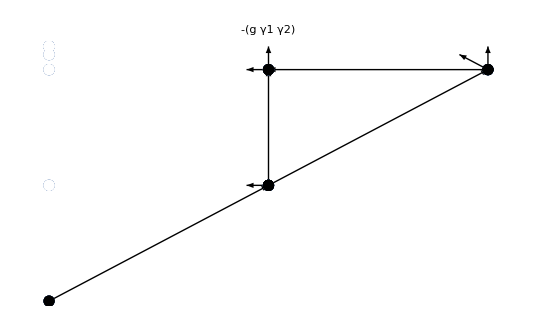

```mathematica
ListPlot[dots,
PlotLabel->ToString[ weight],
Axes->False,
Frame->False,
Mesh->Full,
(*AxesOrigin->dots[[1]]+0.01,*)
PlotStyle->PointSize[0.015],
Prolog->pureProp]
```

```mathematica
dots={{1,1},{2,1},{2,2}};
styledDots={Style[{1,1},Disk[{0,0},0.1],Black],Style[{2,1},Disk[{0,0},0.1],White],Style[{2,2},Disk[{0,0},0.1],Black]};
ListPlot[styledDots,
Axes->False,
Frame->False,
Mesh->Full,
AxesOrigin->dots[[1]]+0.01,
PlotStyle->PointSize[0.03],
BaseStyle->Arrowheads[{0,.05,0}],
Prolog->{Style[Arrow[dots[[{1,2}]]],Red,Arrowheads[{0,-.05,0}]],
Style[FindArc[dots[[1]],dots[[3]],1][[1]],FindArc[dots[[1]],dots[[3]],1][[2]],Black],
Style[FindArc[dots[[1]],dots[[3]],2][[1]],FindArc[dots[[1]],dots[[3]],2][[2]],Red],
Style[FindArc[dots[[1]],dots[[3]],3][[1]],FindArc[dots[[1]],dots[[3]],3][[2]],Red]}]
```

-Graphics-

#### Tests

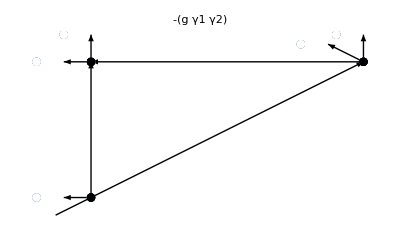

```mathematica
terms=-g γ1 γ2 ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]];
DrawFromContraction[terms]
```

## FindArc[]

```mathematica
ClearAll[FindArc];

FindArc[dot1__,dot2__,order_]:=Module[{sub,px,py,qx,qy,cx,cy,r,radius,centerCoord,c,startAngle,endAngle,circle},

If[order==1,Return[{Arrow[{dot1,dot2}],Arrowheads[{0,.05,0}]}]];

sub={px:>dot1[[1]],py:>dot1[[2]],qx:>dot2[[1]],qy:>dot2[[2]]};

radius=EuclideanDistance[{px,py},{qx,qy}]/(1.07)^order/.sub;
AppendTo[sub,r:>radius];

centerCoord=Solve[{(px-cx)^2+(py-cy)^2==r^2,(qx-cx)^2+(qy-cy)^2==r^2},{cx,cy},Assumptions->r>0];
centerCoord=centerCoord/.sub;

c={cx,cy}/.centerCoord[[Mod[order,2]+1]];


startAngle=ArcTan[px-c[[1]],py-c[[2]]]/.sub;

endAngle=ArcTan[qx-c[[1]],qy-c[[2]]]/.sub;

circle=Circle[c,radius,{startAngle,endAngle}];

Return[{Arrow[circle],Arrowheads[{0,(-1)^Mod[order,2] .05,0}]}];
]
```

```mathematica
listTest={2,3}
Delete[listTest,2][[1]]
```

{2,3}

2

#### Test

```mathematica
ToExpression[StringReplace[ToString[FindArc[dots[[1]],dots[[3]],2]],{"{"->"","}"->"",", "->","}]]
```

ToExpression::sntx: Invalid syntax in or before "Arrow[Circle[0.783833,2.21617,1.23523,-1.39489,-0.175907]],Arrowheads[0,0.05,0]".
                                                                                                            ^

$Failed

```mathematica
Graphics[{Arrow[Circle[{0,0},1,{π,π/2}]]}]
```

-Graphics-

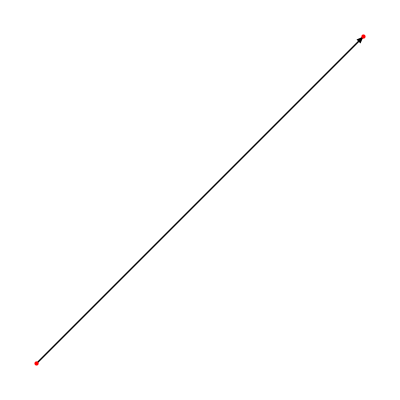

-Graphics-

-Graphics-

```mathematica
Graphics[{Arrow[FindArc[dots[[1]],dots[[3]],1]],Red,Point[dots[[{1,3}]]]}]
Graphics[{Arrow[FindArc[dots[[1]],dots[[3]],2]],Red,Point[dots[[{1,3}]]]}]
Graphics[{Arrow[FindArc[dots[[1]],dots[[3]],3]],Red,Point[dots[[{1,3}]]]}]
```

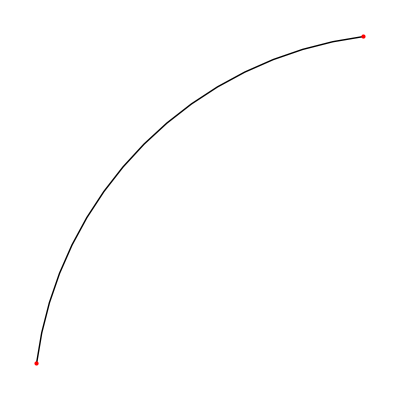

```mathematica
sub={px->dots[[1,1]],py->dots[[1,2]],qx->dots[[3,1]],qy->dots[[3,2]]};
rad=EuclideanDistance[{px,py},{qx,qy}]/(1.07)^3/.sub;
AppendTo[sub,r->rad];
centerCoord=Solve[{(px-cx)^2+(py-cy)^2==r^2,(qx-cx)^2+(qy-cy)^2==r^2},{cx,cy},Assumptions->r>0];
centerCoord/.sub;
c={cx,cy}/.%[[2]];
startAngle=(ArcTan[px-c[[1]],py-c[[2]]])/.sub;
endAngle=(ArcTan[qx-c[[1]],qy-c[[2]]])/.sub;

Graphics[{Circle[c,rad,{startAngle,endAngle}],Red,Point[dots[[{1,3}]]]}]
```

## ToMomentumSpace

## WORKING HERE

```mathematica
ClearAll[ToMomentumSpace];
Options[ToMomentumSpace]={"print"->False,"mχ"->m2χ,"mϕ"->m2ϕ,"amputateLegs"->{χs}};

ToMomentumSpace[exp_,OptionsPattern[]]:=Module[{terms,pureProp,externalLegs,weight,momentumExp,i,j,m2χ,m2ϕ,ptot},
ptot=0;
m2χ=OptionValue["mχ"];
m2ϕ=OptionValue["mϕ"];

If[OptionValue["print"],
Print[Style["\t Mass values: ",{Blue}],"mχ = ",OptionValue["mχ"],", mϕ = ",OptionValue["mϕ"] ]
];


terms=exp//.F_[A___,Subscript[x, a_],B___]Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>F[A,Subscript[x, b],B]Subscript[G, ψ][Subscript[x, a],Subscript[x, b],Subscript[t, c]]/.Subscript[G, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>Subscript[G, ψ][Subscript[x, b],Subscript[x, b],Subscript[t, c]];
terms=List @@ (terms);

pureProp=Delete[terms,1];
pureProp=DeleteElements[pureProp,{g,γ1,γ2,γ1g,γ2g}];

externalLegs= DeleteElements[pureProp,{Subscript[G, _][___]}];

weight=Times@@DeleteElements[terms,pureProp];

For[i=1, i<=Length[pureProp],i++,
pureProp[[i]]=pureProp[[i]]/.{Subscript[F_, ϕ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>(1/(γ(s[Subscript[p, i]]+m2ϕ)))^n δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c-1]],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, 0],Subscript[t, c_]]:>ϕ[k]δ[k,Subscript[x, a],Subscript[t, c]],
Subscript[F_, ϕ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>1/(γ(s[Subscript[p, i]]+m2ϕ))δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c-1]],

Subscript[F_, χ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>(1/(s[Subscript[p, i]]+m2χ))^n δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c]],
Subscript[F_, χ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>1/(s[Subscript[p, i]]+m2χ)δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c]],

Subscript[F_, ψ]^n_[Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c-1]],
Subscript[F_, ψ][Subscript[x, a_],Subscript[x, b_],Subscript[t, c_]]:>δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]]δ[-Subscript[p, i],Subscript[x, b],Subscript[t, c-1]],

χs[Subscript[x, a_],___,Subscript[t, c_]]:>χs[Subscript[p, i]]δ[Subscript[p, i],Subscript[x, a],Subscript[t, c]],
ϕs[Subscript[x, a_],Subscript[t, c_]]:>ϕs[Subscript[p, i]]δ[Subscript[p, i],Subscript[x, a],Subscript[t, c-1]],
ψs[Subscript[x, a_],Subscript[t, c_]]:>ψs[Subscript[p, i]]δ[Subscript[p, i],Subscript[x, a],Subscript[t, c-1]]};
ptot+=Subscript[p, i]
];

momentumExp = Times@@pureProp;
momentumExp=momentumExp*WannaBeDiracDelta[ptot+k];

If[OptionValue["print"],
Print[Style["\n\t Expression in momentum space, not yet integrated:\n",{Blue}],momentumExp ]
];


(* VERTEX MOMENTUM CONSERVATION *)
momentumExp=momentumExp//.δ[a_,A___]δ[ Subscript[p, b_],A___]:>δ[a+ Subscript[p, b],A]//.δ[a_,A___]δ[- Subscript[p, b_],A___]:>δ[a- Subscript[p, b],A]/.δ[a_+Subscript[p, b_],A___]:>DiracDelta[a+ Subscript[p, b]]ⅆ Subscript[p, b];

If[OptionValue["print"],
Print[Style["\n\t Setting up momentum conservation\n",{Blue}],momentumExp ]
];

For[i=1, i<=Length[pureProp],i++,
If[!FreeQ[momentumExp,ⅆ Subscript[p, i]],
momentumExp=Integrate[momentumExp /.ⅆ Subscript[p, i]->1,{Subscript[p, i],-∞,∞},GenerateConditions->False];
]
];


If[OptionValue["print"],
Print[Style["\n\t Implementing momentum conservation at vertices\n",{Blue}],momentumExp ]
];

(* TOTAL MOMENTUM CONSERVATION *)
momentumExp=momentumExp/.WannaBeDiracDelta[a_+Subscript[p, b_]]:>DiracDelta[a+Subscript[p, b]]ⅆ Subscript[p, b];

If[OptionValue["print"],
Print[Style["\n\t Setting up TOTAL momentum conservation\n",{Blue}],momentumExp ]
];

For[i=1, i<=Length[pureProp],i++,
If[!FreeQ[momentumExp,ⅆ Subscript[p, i]],
momentumExp=Integrate[momentumExp /.ⅆ Subscript[p, i]->1,{Subscript[p, i],-∞,∞},GenerateConditions->False];
]
];

If[OptionValue["print"],
Print[Style["\n\t Implementing TOTAL momentum conservation\n",{Blue}],momentumExp ]
];

(* MOMENTA REORDERING *)
j=Length[pureProp];
For[i=1, i<=Length[externalLegs],i++,
While[FreeQ[momentumExp,Subscript[p, i]],
momentumExp=momentumExp/.Subscript[p, j]->Subscript[p, i];
j--;
];
];

If[OptionValue["print"],
Print[Style["\n\t Reordering momenta\n",{Blue}],momentumExp ]
];

(* LEG AMPUTATION *)
If[Length[OptionValue["amputateLegs"]]=!=0,
For[i=1, i<=Length[OptionValue["amputateLegs"]],i++,

momentumExp=momentumExp/.OptionValue["amputateLegs"][[i]][a_+Subscript[p, b_]]:>OptionValue["amputateLegs"][[i]][a+Subscript[p, b]]WannaBeDiracDelta[a+Subscript[p, b]]ⅆ Subscript[p, b]/.OptionValue["amputateLegs"][[i]][a_-Subscript[p, b_]]:>OptionValue["amputateLegs"][[i]][a-Subscript[p, b]]WannaBeDiracDelta[a-Subscript[p, b]]ⅆ Subscript[p, b]/.OptionValue["amputateLegs"][[i]][Subscript[p, b_]]:>OptionValue["amputateLegs"][[i]][Subscript[p, b]]WannaBeDiracDelta[Subscript[p, b]]ⅆ Subscript[p, b];
];


(*
momentumExp=momentumExp//.WannaBeDiracDelta[a_]WannaBeDiracDelta[c_+Subscript[p, b_]]/;(!FreeQ[a,Subscript[p, b]]):>WannaBeDiracDelta[a-Subscript[p, b]-c]//.WannaBeDiracDelta[a_]WannaBeDiracDelta[c_-Subscript[p, b_]]/;(!FreeQ[a,Subscript[p, b]]):>WannaBeDiracDelta[a-Subscript[p, b]+c]/.WannaBeDiracDelta[a_+Subscript[p, b_]]:>DiracDelta[a+Subscript[p, b]]ⅆ Subscript[p, b]/.WannaBeDiracDelta[a_-Subscript[p, b_]]:>DiracDelta[a-Subscript[p, b]]ⅆ Subscript[p, b];


Print["\n",momentumExp,"\n"];
*)

momentumExp=momentumExp/.WannaBeDiracDelta[a_+c_ Subscript[p, b_]+d_ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[a+c Subscript[p, b]+d Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b]/.WannaBeDiracDelta[c_ Subscript[p, b_]+d_ Subscript[p, e_]](ⅆ Subscript[p, b_])^2:> WannaBeDiracDelta[c Subscript[p, b]+d Subscript[p, e]]ⅆ Subscript[p, e] ⅆ Subscript[p, b];

If[OptionValue["print"],
Print[Style["\n\t Setting up the amputation ofthe fields ",{Blue}],Style[OptionValue["amputateLegs"],{Blue}],"\n",momentumExp,"\n"];
];

For[j=1, j<=Length[externalLegs],j++,
If[!FreeQ[momentumExp,ⅆ Subscript[p, j]],

momentumExp=momentumExp /.{WannaBeDiracDelta[a_]/;(!FreeQ[a,Subscript[p, j]] ):>DiracDelta[a],ⅆ Subscript[p, j]->1}//.DiracDelta[a_]DiracDelta[b_]/;(!FreeQ[a,Subscript[p, j]] && !FreeQ[b,Subscript[p, j]]):>WannaBeDiracDelta[a]DiracDelta[b];
momentumExp=Integrate[momentumExp,{Subscript[p, j],-∞,∞},GenerateConditions->False];
]
];

If[OptionValue["print"],
Print[Style["\n\t Amputating the fields ",{Blue}],Style[OptionValue["amputateLegs"],{Blue}],Style[" \n",{Blue}],momentumExp ]
];
];


If[OptionValue["print"],Print["\n"]];

Return[momentumExp];
]
```

#### Attempts

```mathematica
momentumExp=(Subscript[p, 1]+Subscript[p, 2])DiracDelta[Subscript[p, 1]+Subscript[p, 2]+Subscript[p, 3]]ⅆ Subscript[p, 1];
For[i=1, i<=3,i++,
If[!FreeQ[momentumExp,ⅆ Subscript[p, i]],
momentumExp=Integrate[momentumExp /.ⅆ Subscript[p, i]->1,{Subscript[p, i],-∞,∞},GenerateConditions->False];
]
];
momentumExp
```

-p_3

```mathematica
ptot=Subscript[p, 1]+Subscript[p, 2];
momentumExp=ptot DiracDelta[Subscript[p, 1]+Subscript[p, 2]+Subscript[p, 3]]ⅆptot;
Integrate[momentumExp /.ⅆptot->1,{ptot,-∞,∞},GenerateConditions->False]
```

Integrate::ilim: Invalid integration variable or limit(s) in {p_1+p_2,-∞,∞}.

Integrate[DiracDelta[p_1+p_2+p_3] (p_1+p_2),{p_1+p_2,-∞,∞},GenerateConditions→False]

#### Test

```mathematica
exp=-g γ1 γ2 ϕs[Subscript[x, 2],Subscript[t, 3]] Subscript[G, χ][Subscript[x, 3],Subscript[x, 2],Subscript[t, 2]] χs[Subscript[x, 1],1,2,Subscript[t, 1]] χs[Subscript[x, 3],1,2,Subscript[t, 2]] ψs[Subscript[x, 2],Subscript[t, 3]] ψs[Subscript[x, 3],Subscript[t, 3]] Subscript[G, ϕ][Subscript[x, 1],Subscript[x, 0],Subscript[t, 1]] Subscript[G, ϕ][Subscript[x, 2],Subscript[x, 1],Subscript[t, 2]] Subscript[G, ψ][Subscript[x, 3],Subscript[x, 1],Subscript[t, 2]];
ToMomentumSpace[exp,"print"->False,"amputateLegs"->{χs,ψs}]
```

(ϕ[k] ϕs[-k] χs[0]^2 ψs[0]^2)/(γ (m2ϕ+s[p_3]) (m2χ+s[-k+p_3]))

```mathematica
(* ok it seems to be working *)
```